## 2 species system with death: exploration

## Calculating velocity without any assumptions or simplification

```mathematica
ClearAll["Global`*"]
 (*definition of determinant as a function of s and k *)
det2spA[s_,k_]:=Det[({{s+v1* k, 0}, {0, s+v2*k}})-({{r1-f1, f2}, {f1, r2-f2}})]
det3spA[s_,k_]:=Det[({{s+v1* k, 0, 0}, {0, s+v2* k, 0}, {0, 0, s+v3* k}})-({{r1-f1, f2, 0}, {f1, r2-f2, f3}, {0, f3, r3-f3}})]

dkDet2spA[s_,k_]:=Dt[det2spA[s,k],k, Constants->{v1,v2, f1,f2,r1,r2}]/.Dt[s,k,Constants->{v1,v2, f1,f2,r1,r2}]->s/k
dkDet3spA[s_,k_]:=Dt[det3spA[s,k],k, Constants->{v1,v2, v3, f1,f2, f3,r1,r2, r3}]/.Dt[s,k,Constants->{v1,v2, v3, f1,f2, f3,r1,r2, r3}]->s/k


eqnForS2sp[s_,k_]:=Collect[2*det2spA[s,k] -k*dkDet2spA[s,k],s]
eqnForS3sp[s_,k_]:=Collect[3*det3spA[s,k] -k*dkDet3spA[s,k],s]
velocity[s_,k_]:=-s/k
```

## Exploring the velocity jump: 2 species

```mathematica
skRoots2sp=Solve[{det2spA[s,k]==0,eqnForS2sp[s,k]==0},{s,k}];
(*2sp*)
s12sp=s/.skRoots2sp[[1]];
k12sp=k/.skRoots2sp[[1]];
s22sp=s/.skRoots2sp[[2]];
k22sp=k/.skRoots2sp[[2]];
v12sp=velocity[s12sp,k12sp];
v22sp=velocity[s22sp,k22sp];
```

The velocity at the transition from imaginary to real velocity is given by  J_{effective} which is the weighted average of the velocities with weights (r1-f1) and (r2-f2) where r1 is the net growth/death rate.

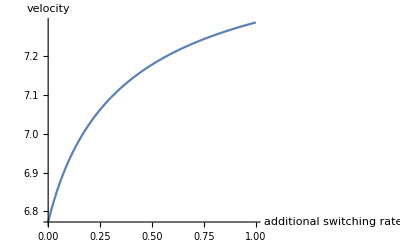

```mathematica
Jeff=((r1-f1)*v2+(r2-f2)*v1)/ (r1-f1+r2-f2);

f10=0.1;
f20=1.;
v10=5;
v20=10.;
r10=0.4;
r20=-0.4;
vel1[g_,f_]:=v12sp/.{f1->f+f10,f2->f+f20,v1->v10,v2->v20,r1->r10+g,r2->r20+g};
vel2[g_,f_]:=v22sp/.{f1->f+f10,f2->f+f20,v1->v10,v2->v20,r1->r10+g,r2->r20+g};
(*Plot[{vel1[0.,f],vel2[0,f]},{f,0,1}]*)
Plot[Max[{vel1[0.,f],vel2[0,f]}],{f,0,1},AxesLabel->{"additional switching rate","velocity"}]
```

### Simplify functions for plotting in python

We simplify the expressions for the following case:

The faster species is 1, it moves to the right and dies on average.
The slower species grows. 
So
v1>0, v1+ v2>0
 r1<0, r2>0
 f1 and f2 >0
   We multiply by the sign function instead of dividing

```mathematica
vel1PythonSimple=FullSimplify[v12sp, {v1>0,v1 +v2>0, r1<0, r2>0, f1>0,f2>0}]
vel2PythonSimple=FullSimplify[v22sp, {v1>0,v1 +v2>0, r1<0, r2>0, f1>0,f2>0}]
```

((f2 r1+(f1-r1) r2) (-f2 v1+r2 v1+(f1-r1) v2)+(√(f1 f2 (f2 r1+(f1-r1) r2)) (f2 v1-r2 v1+(f1-r1) v2))/Sign[(f1+f2-r1-r2) (v1-v2)])/((f1-f2-r1+r2) (f2 r1+(f1-r1) r2)+((f1+f2-r1-r2) √(f1 f2 (f2 r1+(f1-r1) r2)))/Sign[(f1+f2-r1-r2) (v1-v2)])

-((f2 r1+(f1-r1) r2) (f2 v1-r2 v1-f1 v2+r1 v2)+(√(f1 f2 (f2 r1+(f1-r1) r2)) (f2 v1-r2 v1+f1 v2-r1 v2))/Sign[(f1+f2-r1-r2) (v1-v2)])/((f1-f2-r1+r2) (f2 r1+(f1-r1) r2)+((-f1-f2+r1+r2) √(f1 f2 (f2 r1+(f1-r1) r2)))/Sign[(f1+f2-r1-r2) (v1-v2)])

### Plot illustrating the death rate means that a positive velocity solution appears abruptly.

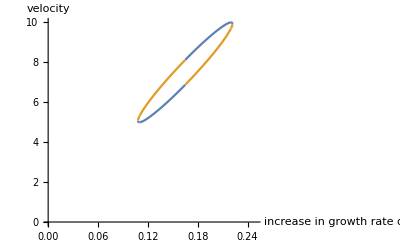

```mathematica
f10=0.0;
f20=0.01;
v10=5;
v20=10.;
r10=-0.1;
r20=-0.2;
vel1[g_,f_]:=v12sp/.{f1->f+f10,f2->f+f20,v1->v10,v2->v20,r1->r10+g,r2->r20+g};
vel2[g_,f_]:=v22sp/.{f1->f+f10,f2->f+f20,v1->v10,v2->v20,r1->r10+g,r2->r20+g};

Plot[{vel1[g,0.01],vel2[g,0.01]},{g,0,0.25}, PlotRange->{{0,0.25},{0,10.0}},AxesLabel->{"increase in growth rate of both species ","velocity"}]
```